# Additional Questions

## T/F

## It is possible to know the exact Energy of a particle at specific time if m<<1.

### False

Uncertainty Principle: ΔE Δt ≥ ℏ

## The wavefunction of a particle gives some information about the position.

### True

|Ψ|^2 gives the probability of finding the particle at some position

## Beta decay involves the nucleus loosing either protons or neutrons.

### True

“Beta decay (β-decay) is a type of radioactive decay in which a beta ray (fast energetic electron or positron) and a neutrino are emitted from an atomic nucleus. For example, beta decay of a neutron transforms it into a proton by the emission of an electron, or conversely a proton is converted into a neutron by the emission of a positron (positron emission), thus changing the nuclide type.”

Takeaway: It looses one, which one it looses depends on the decay β^+→ proton transforms into neutron by emission of positron , β^+→ neutron transforms into proton by emission of electron)

## The element _12^25 Mg has 12 neutrons in its nucleus.

### False

Protons: Z=12
Atomic Mass: A=25
Neutrons = A-Z=13

## Calculations

## For an electron, using quantum numbers {n, l, m_l,m_s}, if n=1,2,3,4,5 how many unique combinations exist?

### 110

Relationships:
l=0,...,n-1
m_l=-l,...,0,...l
m_s=-1/2,1/2
we could write the solutions by hand or utilize series to represent the number or states
Relationships:
n→ (∑_1)^3
l→ (∑_0)^(n-1)
m_l→ (∑_-l)^l
m_s→ 2

```mathematica
2 ∑_(n=1)^5 ∑_(l=0)^(n-1) ∑_(ml=-l)^l 1
```

110

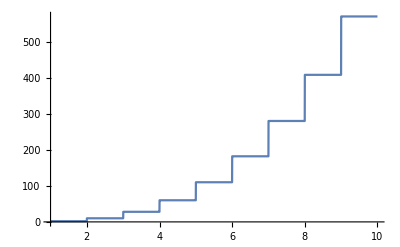

```mathematica
Plot[2 ∑_(n=1)^x ∑_(l=0)^(n-1) ∑_(ml=-l)^l 1,{x,1,10}]
```

## The galaxy EGS-zs8-1 lies 13.1 billion light-years from Earth, the largest distance ever measured between Earth and another galaxy (May 5^th 2015). How fast is this galaxy receding from earth?

### 2.7248×10^8 m/s

Hubble’s law is a statement of a direct correlation between the distance to a galaxy and its recessional velocity as determined by the red shift.

Red Shift:
The light from distant stars and more distant galaxies is not featureless, but has distinct spectral features characteristic of the atoms in the gases around the stars. When these spectra are examined, they are found to be shifted toward the red end of the spectrum. This shift is apparently a Doppler shift and indicates that essentially all of the galaxies are moving away from us. Using the results from the nearer ones, it becomes evident that the more distant galaxies are moving away from us faster. This is the kind of result one would expect for an expanding universe. The red line of the spectrum below is the transition from n=3 to n=2 of hydrogen and is famous as the H-alpha line seen throughout all the universe.

Hubble’s Equation
v=H_0d
H_0=20.8 km/(s Mly)

```mathematica
d=13.1*10^3; (* Mly *)
H0=20.8; (* km/(s Mly) *)
v=H0 d (* km/s *)
```

272480.